```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
lT=20;
startT=1;
alist=Table[Flatten[Import["bdata/b"<>ToString[i]<>".dat"]],{i,1,lT}];
alist1=Table[Rest[alist[[i]]],{i,1,lT}];
V1=Flatten[Transpose[Table[Flatten[Import["./dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
ρmin=0.;
ρmax=30000.;
```

```mathematica
driv1=Table[Re[SetPrecision[Sum[alist1[[i]][[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,50}]+1/2 First[alist[[i]]],100]/.{ρ->0}],{i,1,lT}];
```

```mathematica
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[10])/lT*(i-1)]//N,{i,1,lT}];
slop=Table[{SetPrecision[Log[T[[i]]/125.9556],90],SetPrecision[Re[FindFit[Transpose[{-Log[T/125.9556],Log[1/√driv1]}][[i;;i+1]],a x+b,{a,b},x][[1]][[2]]],90]},{i,1,lT-1}];
```

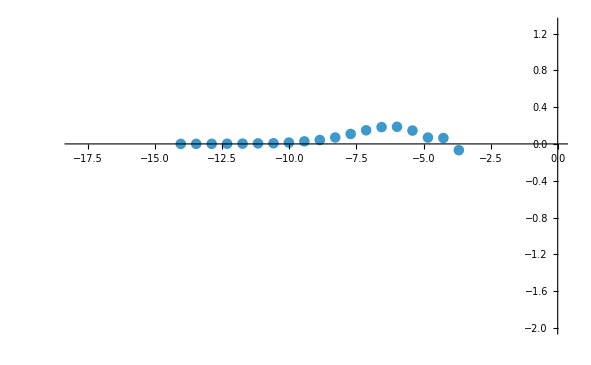

```mathematica
ListPlot[slop,ScalingFunctions->{Automatic,Automatic},PlotRange->{{-18,0},{-2.,1.3}}]
```